# Simplest Pivoting

## Gaussian Elimination

```mathematica
A=N[{
{1,2,3},
{4,5,6},
{7,8,10}}];
```

### Column Pivoting

```mathematica
b={10,40,17};
A=N[{
{1,2,3},
{4,5,6},
{7,8,10}}];

m=Length[A];
p=Range[1,m];
ACol = ArrayFlatten[{{A, {b}ᵀ}}]; 
(* Co Pivot *)
{k,j}={1,3};
p⟦{j,k}⟧=p⟦{k,j}⟧;
ACol[[All,{j,k}]]=ACol⟦All,{k,j}⟧;
(* Row Reduce *)
(* Zap the 2nd and 3rd row *)
m = ACol⟦2,1⟧/ ACol⟦1,1⟧;
ACol⟦2⟧=ACol⟦2⟧-m*ACol⟦1⟧;
m = ACol⟦3,1⟧/ ACol⟦1,1⟧;
ACol⟦3⟧=ACol⟦3⟧-m*ACol⟦1⟧;
MatrixForm[ACol]
(* Col Pivot *)
{k,j}={2,3};
p⟦{j,k}⟧=p⟦{k,j}⟧;
ACol[[All,{j,k}]]=ACol⟦All,{k,j}⟧;
MatrixForm[ACol]
(* Row Reduce *)
(* Zap the 3rd row *)
m = ACol⟦3,2⟧/ ACol⟦2,2⟧;
ACol⟦3⟧=ACol⟦3⟧-m*ACol⟦2⟧;
MatrixForm[ACol]
p
```

(3. | 2. | 1. | 10
0. | 1. | 2. | 20.
0. | 1.33333 | 3.66667 | -16.3333)

(3. | 1. | 2. | 10
0. | 2. | 1. | 20.
0. | 3.66667 | 1.33333 | -16.3333)

(3. | 1. | 2. | 10
0. | 2. | 1. | 20.
0. | 0. | -0.5 | -53.)

{3,1,2}

### Complete Pivoting

```mathematica
b={10,40,17};
A=N[{
{1,2,3},
{4,5,6},
{7,8,10}}];
m=Length[A];
p=Range[1,m];
ARow = ArrayFlatten[{{A, {b}ᵀ}}]; 
MatrixForm[ARow];
(* Col Pivot *)
{kc,jc}={1,3};
p⟦{jc,kc}⟧=p⟦{kc,jc}⟧;
ARow[[All,{jc,kc}]]=ARow⟦All,{kc,jc}⟧;
(* Row Pivot *)
{kr,jr}={1,3};
ARow[[{jr,kr},All]]=ARow⟦{kr,jr},All⟧;
MatrixForm[ARow];
(* Row Reduce *)
(* Zap the 2nd and 3rd row *)
m = ARow⟦2,1⟧/ ARow⟦1,1⟧;
ARow⟦2⟧=ARow⟦2⟧-m*ARow⟦1⟧;
m = ARow⟦3,1⟧/ ARow⟦1,1⟧;
ARow⟦3⟧=ARow⟦3⟧-m*ARow⟦1⟧;
ARow=Chop[ARow];
MatrixForm[ARow]
(* Col Pivot *)
{kc,jc}={2,3};
p⟦{jc,kc}⟧=p⟦{kc,jc}⟧;
ARow[[All,{jc,kc}]]=ARow⟦All,{kc,jc}⟧;
(* Row Pivot *)
{kr,jr}={2,3};
ARow[[{jr,kr},All]]=ARow⟦{kr,jr},All⟧;
MatrixForm[ARow]
(* Row Reduce *)
(* Zap the 3rd row *)
m = ARow⟦3,2⟧/ ARow⟦2,2⟧;
ARow⟦3⟧=ARow⟦3⟧-m*ARow⟦2⟧;
ARow=Chop[ARow];
MatrixForm[ARow]
```

(10. | 8. | 7. | 17
0 | 0.2 | -0.2 | 29.8
0 | -0.4 | -1.1 | 4.9)

(10. | 7. | 8. | 17
0 | -1.1 | -0.4 | 4.9
0 | -0.2 | 0.2 | 29.8)

(10. | 7. | 8. | 17
0 | -1.1 | -0.4 | 4.9
0 | 0 | 0.272727 | 28.9091)

```mathematica
LinearSolve[A,b][[p]]
MatrixForm[RowReduce[ARow]]
```

{-53.,-43.,106.}

(1 | 0. | 0. | -53.
0 | 1 | 0. | -43.
0 | 0 | 1 | 106.)

```mathematica
ColPivotFind[k_,A_]:=Module[{},
]
```

The plan is to generate explicit simple pivoting code in Mathematica for Aliyah, Caleb and Josie.

### Code for pivots!

So 
m is the size of the square matrix.  
k is the diagonal entry we are currently on. 
A is the current version of the augmented matrix.

```mathematica
RowPiv[{k_,m_},A_]:=Module[{col},
col=ConstantArray[0.0,m];
col⟦k;;m⟧=A⟦k;;m,k⟧;
FirstPosition[col,Max[col]][[1]]
]
```

```mathematica
ColPiv[{k_,m_},A_]:=Module[{row},
row=ConstantArray[0.0,m];
row⟦k;;m⟧=A⟦k,k;;m⟧;
FirstPosition[row,Max[row]][[1]]
]
```

```mathematica
ColPivAliyah[{k_,m_},A_]:=Module[{row=Abs[A⟦k,1;;m⟧]},
If[k>1,row⟦1;;k-1⟧*=0.0];
FirstPosition[row,Max[row]][[1]]
]
```

```mathematica
CompPiv[{k_,m_},A_]:=Module[{mat},
mat=ConstantArray[0.0,{m,m}];
mat⟦k;;m,k;;m⟧=Abs[A⟦k;;m,k;;m⟧];
FirstPosition[mat,Max[mat]]
]
```

```mathematica
A=N[{
{1,3,2},
{4,-8,68},
{7,-79,10}}];
{k,m}={1,3};
RowPiv[{1,m},A]
ColPiv[{2,m},A]
CompPiv[{1,m},A]
```

3

3

{3,2}

```mathematica
FirstPosition[Abs[A],79.0]
```

{3,2}

## No Pivoting LU

Here is the unpivoted function from class

```mathematica
Clear[LUTogether]
LUTogether[A_]:=Module[{m=Length[A],LU=A},
Do[


Do[
LU⟦j,k⟧=LU⟦j,k⟧/LU⟦k,k⟧;
(* Note the diagonals store the U not the L *)
LU⟦j,k+1;;m⟧-=LU⟦j,k⟧ LU⟦k,k+1;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Splitting LU to maintain the return values *)
{LowerTriangularize[LU,-1]+IdentityMatrix[m],UpperTriangularize[LU]}
]
```

I am going to just look at this as a script.

2.28878×10^-16

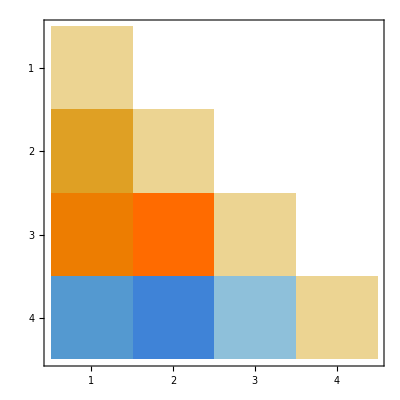
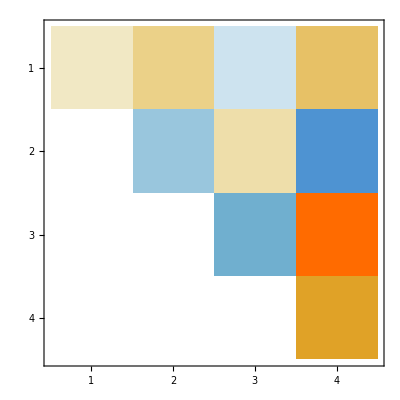

```mathematica
m=4;
A=RandomReal[{-1,1},{m,m}]; b=RandomReal[{-1,1},m];
(* Start Script *)
LU=A;
Do[
Do[
LU⟦j,k⟧=LU⟦j,k⟧/LU⟦k,k⟧;
(* Note the diagonals store the U not the L *)
LU⟦j,k+1;;m⟧-=LU⟦j,k⟧ LU⟦k,k+1;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Splitting LU to maintain the return values *)
{L,U}={LowerTriangularize[LU,-1]+IdentityMatrix[m],UpperTriangularize[LU]};
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

I think it is the bookkeeping that is messing folks up.  Lets just do Gauss Elimination without any book keeping

## No Bookkeeping Gaussian Elimination

I think it is the bookkeeping that is messing folks up.  Lets just do Gauss Elimination without any book keeping. Here is an unpivoted forward elimination for Gaussian elimination.

```mathematica
m=4;
A=RandomReal[{-1,1},{m,m}]; b=RandomReal[{-1,1},m];
(* Augmenting the Matrix *)
Aug=ArrayFlatten[{{A,{b}ᵀ}}];
Do[
Do[
Aug⟦j,All⟧-=Aug⟦j,k⟧/Aug⟦k,k⟧ Aug⟦k,All⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Looking at what is left of the Augmented Matrix *)
MatrixForm[Chop[Aug]]
```

(0.760073 | 0.384259 | -0.288141 | 0.345916 | -0.991239
0 | 1.10861 | 0.23815 | 0.141463 | -0.837436
0 | 0 | 1.06942 | 0.92586 | -1.34542
0 | 0 | 0 | 0.584672 | 0.479991)

Lets add row pivoting.

```mathematica
m=4;
A=RandomReal[{-1,1},{m,m}]; b=RandomReal[{-1,1},m];
(* Augmenting the Matrix *)
Aug=ArrayFlatten[{{A,{b}ᵀ}}];
Do[
(* Find largest element in column *)
(* Switch rows *)
Do[
Aug⟦j,All⟧-=Aug⟦j,k⟧/Aug⟦k,k⟧ Aug⟦k,All⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Looking at what is left of the Augmented Matrix *)
MatrixForm[Chop[Aug]]
```